This script determines how much a scattered two photon state overlaps with its initial wavefunction. This is used as a check for the numerics we are doing.

```mathematica
ψ[x_,σ_]:=(ⅇ^(-x^2/(2 σ^2)))/(√(σ √π));
Integrate[ψ[x,σ]^2,{x,-∞,∞},Assumptions->{σ>0}]
```

1

```mathematica
ψT[x_,σ_]:=Evaluate[Integrate[ⅇ^(-y/2)ψ[x+y,σ],{y,0,∞},Assumptions->{σ>0}]];
ψout[x_,σ_]:=ψ[x,σ]-ψT[x,σ];
Integrate[ψout[x,σ]^2,{x,-∞,∞},Assumptions->{σ>0}]
```

1

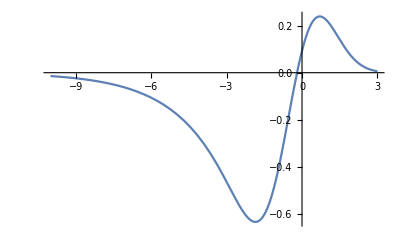

```mathematica
Plot[ψout[x,1],{x,-10,3}]
```

```mathematica
ψ2[x_,y_,σ_]:=ψout[x,σ]ψout[y,σ]-ⅇ^(-Abs[x-y]/2)ψT[Max[x,y],σ]^2;
NIntegrate[ψ2[x,y,1]^2,{x,-∞,∞},{y,-∞,∞}]
```

1.

```mathematica
Plot3D[ψ2[x,y,1],{x,-5,3},{y,-5,3},PlotRange->Full]
```

-Graphics3D-

```mathematica
With[{σ=1},
NIntegrate[ψ2[x,y,σ]ψ[x,σ]ψ[y,σ],{x,-∞,∞},{y,-∞,∞}]
]
```

-0.639387

```mathematica
With[{σ=1},
NIntegrate[ψ2[x,y,σ]ψout[x,σ]ψout[y,σ],{x,-∞,∞},{y,-∞,∞}]
]
```

-0.17789

```mathematica
0.639387^2
```

0.408816